## Объявление глобальных переменных

```mathematica
SetDirectory["/Users/kirillivanov/Documents/Code/For Geant analysis/a-fe_g-ne/"]
print@x_:=(Print@x;x);
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

/Users/kirillivanov/Documents/Code/For Geant analysis/a-fe_g-ne

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 17.3761 | 0.1917
1000. | 0. | 37.7396 | 0.270753
2000. | 0. | 77.4087 | 0.408148
3000. | 0. | 117.779 | 0.489602
4000. | 0. | 157.75 | 0.583861
5000. | 0. | 199.923 | 0.65227
6000. | 0. | 239.543 | 0.698525
7000. | 0. | 280.389 | 0.733385
8000. | 0. | 318.297 | 0.769299
9000. | 0. | 359.931 | 0.836299
10000. | 0. | 398.18 | 0.888064

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-3.41184+0.0407805 x-5.57235×10^-8 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -3.41184 | 0.7433 | -4.59013 | 0.00177826
x | 0.0407805 | 0.000343977 | 118.556 | 2.86385×10^-14
x^2 | -5.57235×10^-8 | 3.24271×10^-8 | -1.71842 | 0.124042

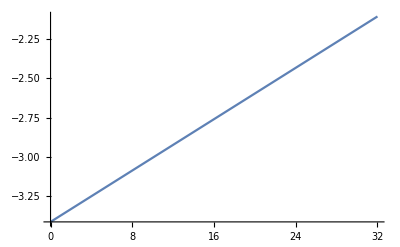

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

{0.411661,0.426753,-0.517506,-0.64906,-1.06866,0.825973,0.278489,1.06799,-0.96833,0.8327,-0.640018}

{0.1917,0.270753,0.408148,0.489602,0.583861,0.65227,0.698525,0.733385,0.769299,0.836299,0.888064}

{4.61142,2.48432,1.60767,1.75745,3.35009,1.60353,0.158947,2.12067,1.58437,0.991413,0.519391}

2.59866

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

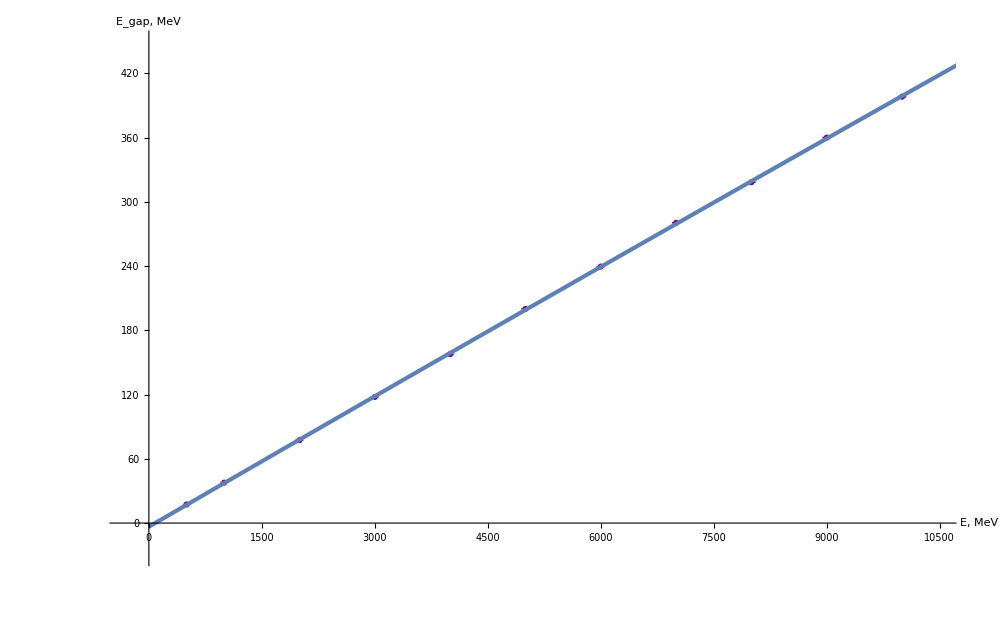

images/png/calib2.png

images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,450}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["images/png/calib2.png",plot2,"PNG"]
Export["images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
Export["fit_res2.csv",exportE,"CSV"]
```

{{-3.41184,0.0407805,-5.57235×10^-8},{0.7433,0.000343977,3.24271×10^-8},2.59866}

fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
893.291 | 8.46155 | 0.226087 | 0.00470322
1370.26 | 9.85141 | 0.189191 | 0.00372886
1950.35 | 12.7099 | 0.16179 | 0.00315305
2904.4 | 15.8513 | 0.135003 | 0.00260747
3519. | 17.337 | 0.120182 | 0.00228781
4122.81 | 19.0209 | 0.114803 | 0.00217063
4995.45 | 20.3005 | 0.1014 | 0.00190946
6288.23 | 23.16 | 0.0915643 | 0.00171123
7150.9 | 23.8457 | 0.0855772 | 0.00159785
7988.05 | 26.4556 | 0.0800065 | 0.00148823
9802.64 | 26.7754 | 0.0742873 | 0.00137148

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00852034+6.63051/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00852034 | 0.00216812 | 3.92983 | 0.00345895
1/(√x) | 6.63051 | 0.114281 | 58.0195 | 6.76017×10^-13

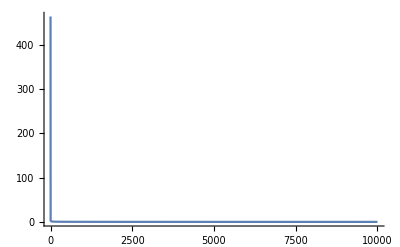

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

{-0.00427914,0.00154996,0.00313155,0.00345019,-0.000111627,0.00301811,-0.000933026,-0.000570797,-0.00135232,-0.00270062,-0.00120228}

{0.00470322,0.00372886,0.00315305,0.00260747,0.00228781,0.00217063,0.00190946,0.00171123,0.00159785,0.00148823,0.00137148}

{0.827793,0.172778,0.986409,1.75085,0.00238066,1.9333,0.238763,0.111262,0.716284,3.29296,0.768476}

1.20014

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

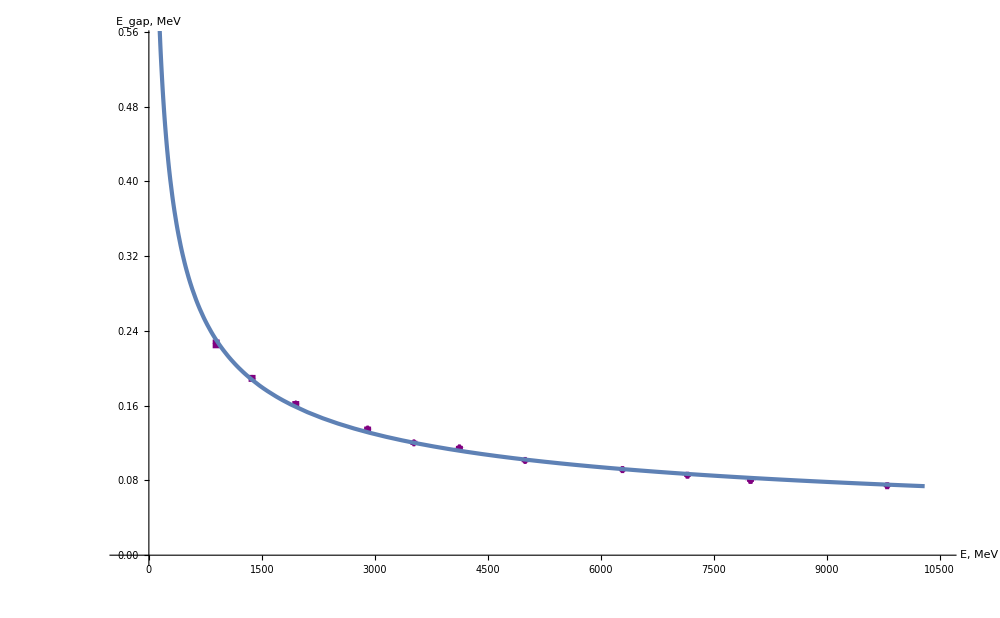

images/png/re.png

images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.55}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["images/png/re.png",plotR,"PNG"]
Export["images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
Export["fit_re_res.csv",exportR,"CSV"]
```

{{0.00852034,6.63051},{0.00216812,0.114281},1.20014}

fit_re_res.csv